```mathematica
α=10; 
β=5;
```

```mathematica
Simplify[e1=Sqrt[α^2-(β+u)^2] - Sqrt[α^2-(β-u)^2]]
```

√(α^2-(β+u)^2)-√(α^2-(u-β)^2)

```mathematica
Series[e1, {u,0,5}]
```

-(2 β u)/(√(α^2-β^2))-(α^2 β u^3)/((α^2-β^2)^(5/2))-(u^5 (α^2 β (3 α^2+4 β^2)))/(4 (α^2-β^2)^(9/2))+O(u^6)

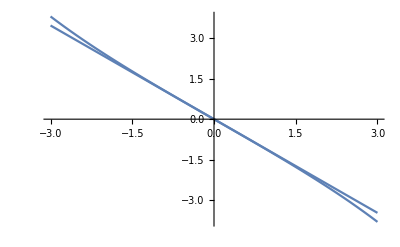

```mathematica
Plot[{e1, Normal[Series[e1, {u,0,1}]]}/.u->x, {x,-3,3}]
```

```mathematica
Clear[α,β, μ1,δ1,μ2,δ2]
```

```mathematica
t1=M[u,α,β,μ1,δ1] M[-u,α,β,μ2,δ2]
```

exp(δ1 (√(α^2-β^2)-√(α^2-(β+u)^2))+δ2 (√(α^2-β^2)-√(α^2-(β-u)^2))+μ1 u-μ2 u)

```mathematica
t2=M[u,α,β,μ1-μ2-(2 δ2 β)/(√(α^2-β^2)),δ1+δ2]
```

exp((δ1+δ2) (√(α^2-β^2)-√(α^2-(β+u)^2))+u (-(2 β δ2)/(√(α^2-β^2))+μ1-μ2))

```mathematica
Table[Simplify[{D[t1,{u,r}]- D[t2,{u,r}]}/.u->0], {r,1,4}]
```

(0
0
-(6 α^2 β δ2)/((α^2-β^2)^(5/2))
(24 α^2 β δ2 (√(α^2-β^2) (μ2-μ1)+β (δ2-δ1)))/((α^2-β^2)^3))